Piecewise[{{0, t≤0}, {1/4 (4 √5+5 ⅇ^((-2-√5) t)-2 √5 ⅇ^((-2-√5) t)-5 ⅇ^((2-√5) t)-2 √5 ⅇ^((2-√5) t)), 0<t≤1}, {1/(4 ⅇ^2)(5 ⅇ^(2+(-2-√5) t)-2 √5 ⅇ^(2+(-2-√5) t)-5 ⅇ^(4+√5+(-2-√5) t)+2 √5 ⅇ^(4+√5+(-2-√5) t)-5 ⅇ^(2+(2-√5) t)-2 √5 ⅇ^(2+(2-√5) t)+5 ⅇ^(√5+(2-√5) t)+2 √5 ⅇ^(√5+(2-√5) t)), True}}]

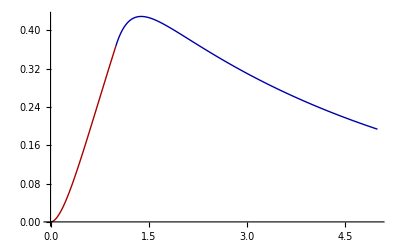

```mathematica
Remove["Global`*"];
τ=1;
a=β/τ;
ω=1;
β=Sqrt[5] ω;
ℱ=Piecewise[{{a,0≤t≤τ}},0];
(*soln1=DSolve[{x1''[t]+2 β x1'[t]+ω^2 x1[t]==a,x1[0]==0,x1'[0]==0},x1[t],t];
x1[t_]=x1[t]/.soln1;*)
soln=DSolve[{x1''[t]+2 β x1'[t]+ω^2 x1[t]==ℱ,x1[0]==0,x1'[0]==0},x1[t],t];
x[t_]=x1[t]/.soln[[1]]
plot1:=Plot[x[t],{t,0,τ},PlotStyle->{Thick,Darker[Red]}]
plot2:=Plot[x[t],{t,τ,5 τ},PlotStyle->{Thick,Darker[Blue]}]
Show[{plot1,plot2},PlotRange->All]
(*Parameter Block
τ=1
a=β/τ;
ω=1;
β=Sqrt[5] ω;*)
(**************)
(*soln2=DSolve[{x2''[t]+2 β x2'[t]+ω^2 x2[t]==0,x2[τ]==x1[τ],x2'[τ]==x1'[τ]},x2[t],t]
x2[t_]=x2[t]/.soln2;
plot1[τ_]:=Plot[x1[t],{t,0,τ},DisplayFunction->Identity,PlotStyle->RGBColor[Sin[τ],4 Cos[τ],Tan[τ]]]
plot2[τ_]:=Plot[x2[t],{t,τ,5τ},DisplayFunction->Identity]
Show[{plot1[1],plot2[1],plot1[2],plot2[2]},PlotRange->All]*)
```